Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210210_impacts_in_time_windows"];
```

```mathematica
data=Import["data_with_time_windows.mx"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

Association Networks in Time Windows

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindows=snetworkdatasingleintimewindows[9,10];]
```

{3.9276,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraphsinglenodes[widthdataintimewindows[[1]][[i]],widthdataintimewindows[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

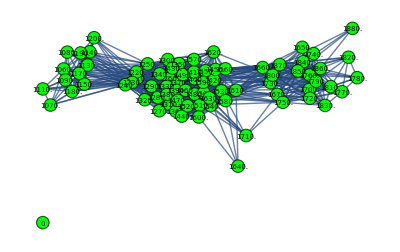
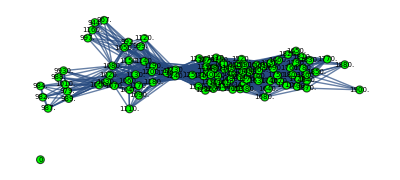
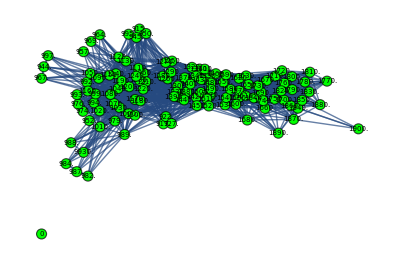
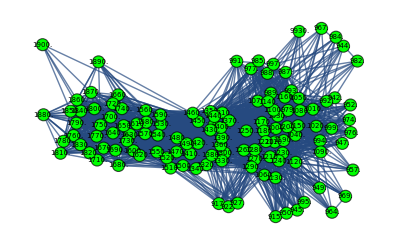
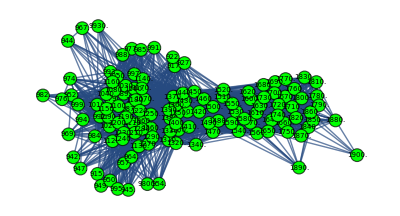
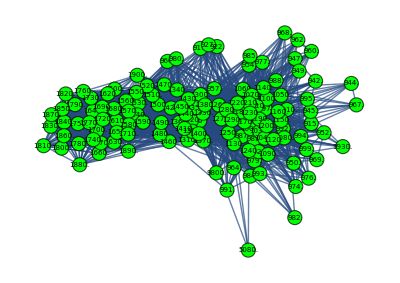
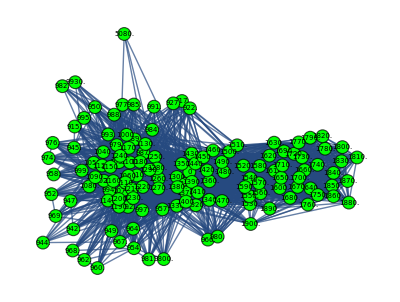
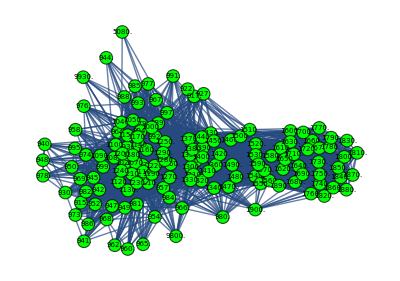
{{-Graphics-,79},{-Graphics-,102},{-Graphics-,119},{-Graphics-,125},{-Graphics-,127},{-Graphics-,133},{-Graphics-,135},{-Graphics-,143},{-Graphics-,144},{-Graphics-,146}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.816837,-0.914287},{0.775318,-0.833272},{0.912826,-0.890899},{0.9729,-0.987608},{0.978297,-0.991312},{0.976393,-0.985596},{0.979992,-0.984999},{0.973833,-0.987195},{0.966704,-0.988102},{0.887562,-0.902762}}

{{0.522385,-0.613315},{0.530661,-0.556155},{0.691093,-0.618492},{0.549054,-0.3911},{0.534222,-0.394403},{0.549708,-0.406185},{0.539973,-0.417934},{0.535635,-0.393469},{0.526522,-0.386032},{0.720341,-0.678254}}

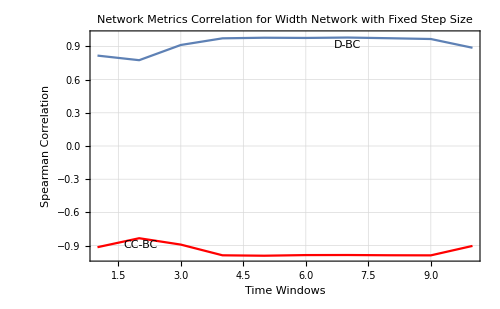
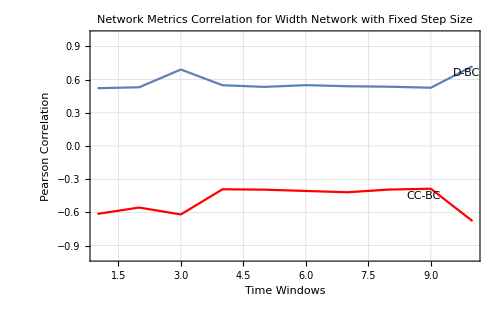

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Width Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-15.3086},{2,-27.6464},{3,-10.1391},{4,-0.619594},{5,0.370311},{6,-0.281378},{7,0.426047},{8,-1.50236},{9,-3.50008},{10,-24.4219}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-5.60894},{2,-5.8892},{3,-6.9099},{4,-7.9931},{5,-7.9275},{6,-7.91104},{7,-8.34481},{8,-8.37427},{9,-7.98517},{10,-7.71136}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-57.9931},{2,-74.5995},{3,-58.4635},{4,-113.126},{5,-126.63},{6,-128.182},{7,-131.784},{8,-156.037},{9,-158.978},{10,-86.3946}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-3.22148},{2,-3.32278},{3,-4.21425},{4,-1.94097},{5,-1.89757},{6,-2.08029},{7,-2.38328},{8,-2.14969},{9,-1.93196},{10,-5.18526}}

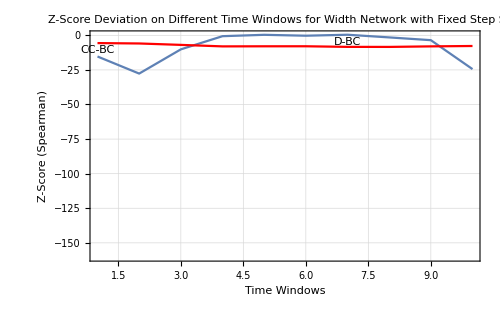
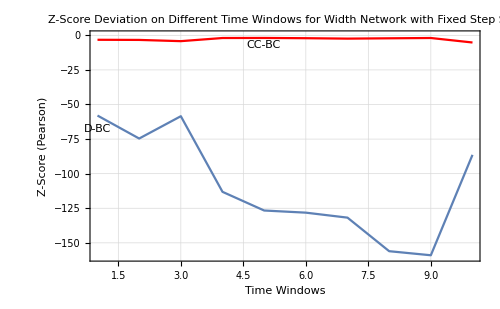

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-160,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-160,0}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Width Network with Fixed Step Size"]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindows=snetworkdatasingleintimewindows[10,10];]
```

{4.35942,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraphsinglenodes[thicknessdataintimewindows[[1]][[i]],thicknessdataintimewindows[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

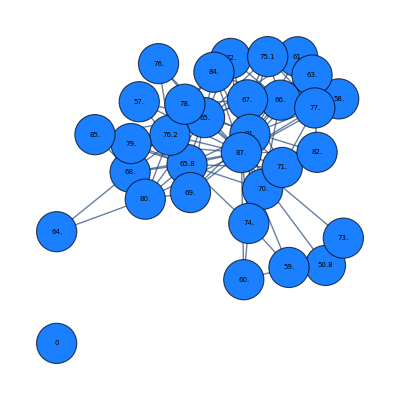
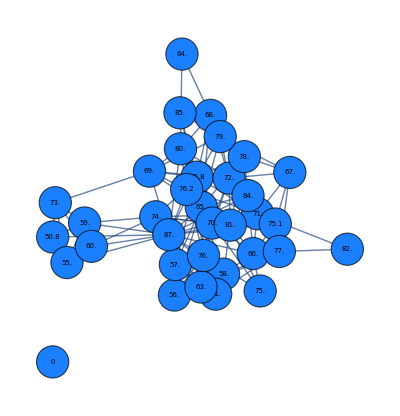
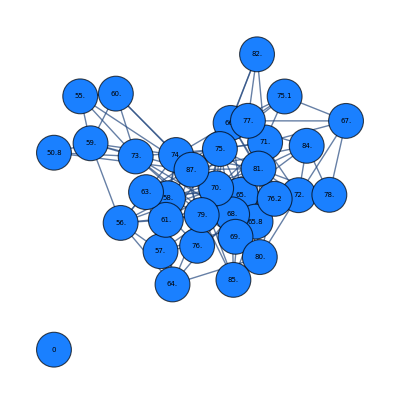
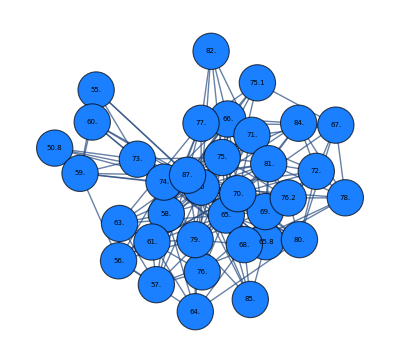
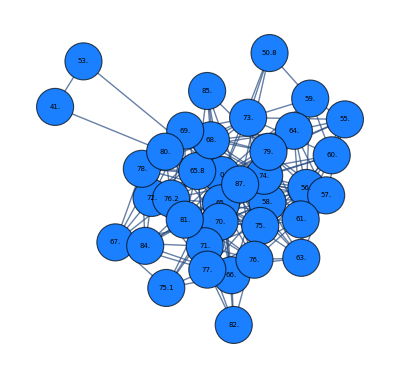
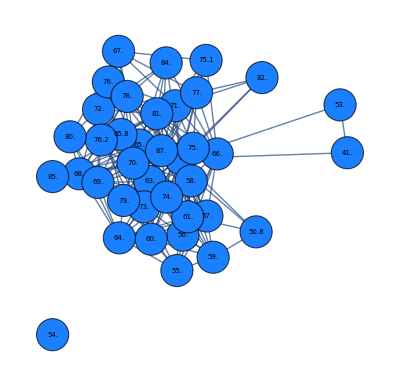
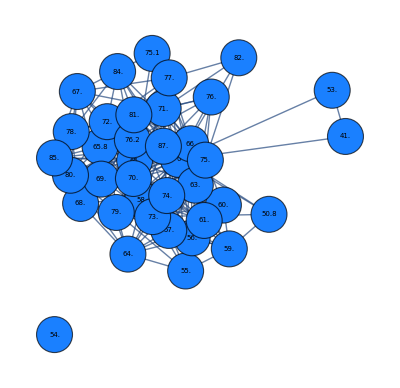
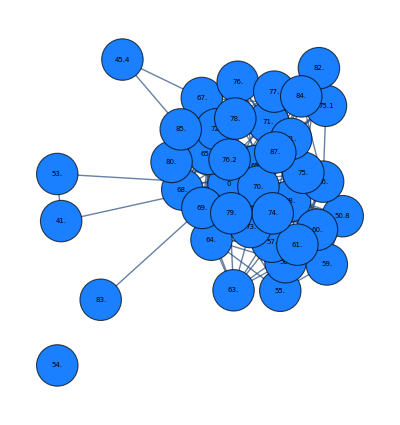
{{-Graphics-,32},{-Graphics-,35},{-Graphics-,35},{-Graphics-,35},{-Graphics-,37},{-Graphics-,38},{-Graphics-,38},{-Graphics-,40},{-Graphics-,41},{-Graphics-,41}}

```mathematica
graphsandnodenumbers
```

```mathematica
correlationvaluesthroughwindowsspearman=Table[correlationfunction[i,1],{i,graphsandnodenumbers[[All,1]]}];
correlationvaluesthroughwindowspearson=Table[correlationfunction[i,2],{i,graphsandnodenumbers[[All,1]]}];
```

```mathematica
correlationvaluesthroughwindowsspearman
correlationvaluesthroughwindowspearson
```

{{0.938808,-0.78658},{0.873987,-0.663998},{0.916719,-0.7004},{0.93912,-0.906811},{0.95285,-0.889666},{0.935017,-0.722435},{0.939483,-0.699436},{0.943043,-0.53645},{0.927237,-0.686511},{0.94354,-0.25778}}

{{0.874484,-0.462631},{0.843387,-0.422115},{0.770286,-0.472945},{0.877292,-0.518271},{0.809918,-0.446188},{0.768257,-0.334724},{0.752032,-0.330238},{0.723693,-0.22225},{0.746908,-0.275495},{0.663251,-0.0583977}}

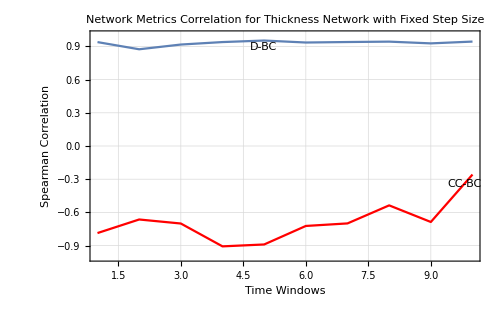
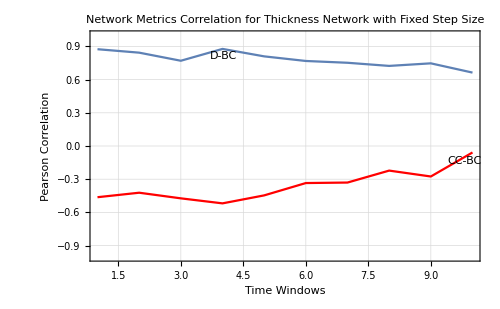

```mathematica
{Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowsspearman[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Spearman Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"],Show[ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,1]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],ListPlot[Transpose[{Range@10,Table[correlationvaluesthroughwindowspearson[[j,2]],{j,1,10}]}],Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Pearson Correlation"}],PlotRange->{All,{-1,1}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Network Metrics Correlation for Thickness Network with Fixed Step Size"]}
```

```mathematica
ZscoreDeBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,0.616193},{2,-1.28733},{3,-0.104282},{4,0.565508},{5,1.07189},{6,0.367045},{7,0.478779},{8,0.559077},{9,-0.0694945},{10,0.590463}}

```mathematica
ZscoreCCBCspearman=Transpose[{Range[1,10],Table[randomnessfunction[i,1],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-2.93182},{2,-2.53266},{3,-2.40751},{4,-3.46177},{5,-3.3986},{6,-2.49543},{7,-2.42854},{8,-1.50394},{9,-2.47674},{10,0.109912}}

```mathematica
ZscoreDeBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,1]]}]
```

{{1,-0.510046},{2,-1.66848},{3,-4.13987},{4,-1.43423},{5,-4.2623},{6,-5.6921},{7,-6.62055},{8,-8.47877},{9,-7.56998},{10,-9.23535}}

```mathematica
ZscoreCCBCpearson=Transpose[{Range[1,10],Table[randomnessfunction[i,2],{i,graphsandnodenumbers[[All,1]]}][[All,2]]}]
```

{{1,-1.57851},{2,-1.33152},{3,-1.32984},{4,-1.33201},{5,-0.9891},{6,-0.2925},{7,-0.278031},{8,0.356254},{9,0.0282377},{10,1.29413}}

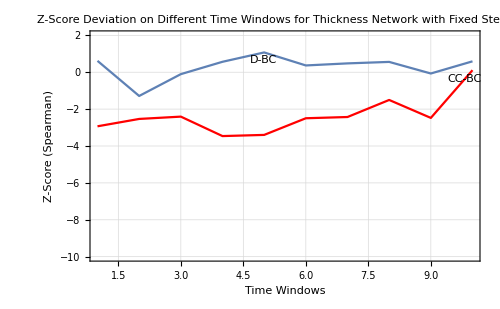
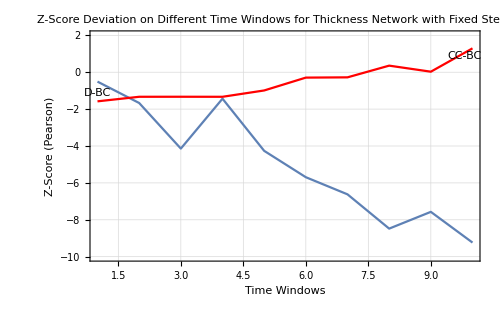

```mathematica
{Show[ListPlot[ZscoreDeBCspearman,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],ListPlot[ZscoreCCBCspearman,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Spearman)"}],PlotRange->{All,{-10,2}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"],Show[ListPlot[ZscoreDeBCpearson,Joined->True,PlotLabels->Placed[{"D-BC"},Top],Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],ListPlot[ZscoreCCBCpearson,Joined->True,PlotLabels->Placed[{"CC-BC"},Top],PlotStyle->Red,Frame->True,FrameLabel->{"Time Windows","Z-Score (Pearson)"}],PlotRange->{All,{-10,2}},Axes->False,ImageSize->500,GridLines->Automatic,PlotLabel->"Z-Score Deviation on Different Time Windows for Thickness Network with Fixed Step Size"]}
```